Lecture 1: PHAS0012 Computing for Mathematical Physics

# Basics of Mathematica

Basics of system: front end and back end: cells: moving around. Saving values. Simple functions.

## A calculator

Simple calculation,

```mathematica
2+2
```

4

Note the In[] and Out[] denoting execution order. They don’t necessarily go in logical order from top to bottom of the notebook - particularly if you go backwards and re-execute earlier commands. Sometimes you want to execute a notebook from top to bottom - see the Evaluation Menu.

% can be used to recall the result of the previous execution. But, this leads to very fragile notebooks - avoid using it!

```mathematica
%+%
```

8

Exact arithmetic: contrast 4/2 and 3/2. Also note more than one command per cell.

```mathematica
4/2
3/2
```

2

3/2

```mathematica
Pi
```

π

```mathematica
Cos[Pi]
Cos[3.14]
```

-1

-0.999999

Note here that a function is called using SQUARE brackets. Mathematica uses the different bracket shapes in special ways. Also note that the function is Cos, not cos: all Mathematica's functions and built-in constants begin with a capital.

```mathematica
I E Pi
```

ⅈ ⅇ π

As an aside, we might ask why Mathematica has to be so fussy about bracket shapes. The answer is that the way we normally write mathematics is ambiguous. For example, if we write f(1+x), do we mean the term 1+x multiplied by f, or is f a function we are applying to 1+x? We have to work it out from the context, knowing whether we have defined a function called f.  Similarly, with a(x,y,z), is a a function that requires three arguments, or are we just scaling a vector given as a list of its components by a scalar, a? In Mathematica there is nothing to prevent us from having functions and variables with the same name, so we need the different bracket conventions to tell Mathematica what we mean.
There is a slight down side to this: we are used to using different bracket styles in large expressions to help us to pair up opening and closing brackets: we might have something like
  {..[(...)/(...) + (..)^2]/[...] + ...},
but in Mathematica all of those term-grouping brackets will have to be ( and ). Luckily Mathematica helps us out a bit when we type, by highlighting brackets that have no opening or closing partner.

Arbitrary precision arithmetic

```mathematica
N[Pi]
N[Pi,100]
```

3.14159

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

It is important to note that Mathematica will keep results exact unless you explicitly tell it not to. For example (Degree is a built-in Mathematica conversion factor from degrees to radians -- note the nice way it prints out):

```mathematica
Sin[30 Degree]
Sin[31Degree]
Sin[29Degree]
```

1/2

Sin[31 °]

Sin[29 °]

The two results which do not have a simple exact form are let unevaluated unless you ask for a numerical result explicitly

```mathematica
N[Sin[30Degree]]
N[Sin[31Degree]]
N[Sin[29Degree]]
```

0.5

0.515038

0.48481

or implicitly

```mathematica
Sin[30.Degree]
Sin[31.Degree]
Sin[29.Degree]
```

0.5

0.515038

0.48481

If you really want to get away from the Sin function and into exact numbers you can do it, but it's probably not very useful in general:

```mathematica
Simplify[FunctionExpand[Sin[29 Degree]]]
```

Sin[(29 π)/180]

## Saving results

A simple equals sign is not the same as a mathematical equals sign. It stores an expression: which can be a number, an expression, a string of characters, or even an equation. In fact, the function which Mathematica uses for the equals sign is the Set function.

```mathematica
x=2
y=15 z + 3
s="Welcome to 2B49"
e=p-1==2
FullForm[Hold[x=2]]
```

2

3+15 z

Welcome to 2B49

-1+p==2

Hold[Set[x,2]]

Note two functions here that can be useful in seeing how Mathematica works: Hold retains an expression without evaluating it, and FullForm shows the full expression as Mathematica holds it.

Note that we can define a mathematical equation, but the equation is defined with a double equals. If both sides of the == can be evaluated, the result will be True or False; if they cannot be evaluated, the expression will be left alone.

```mathematica
1==1
1==2
xval==yval
```

True

False

xval==yval

```mathematica
x
y
s
e
```

2

3+15 z

Welcome to 2B49

-1+p==2

But note that once an assignment is made, it stays there until it is cleared, so that

```mathematica
f=x-1==2
```

False

False, because the result of an == is a logical, true or false, and we'd set x to be 2. We could, though, do

```mathematica
Clear[x]
f=x-1==2
```

-1+x==2

In general, try to avoid setting numerical values using =. We'll see in a later lecture a better way of inserting numerical values.

We can find out about variables using ?

```mathematica
?e
```

Global`e

e=-1+p==2

Note that Mathematica keeps track of the various types of object it can handle by giving them a label, called a Head

```mathematica
Head[x]
Head[y]
Head[s]
Head[e]
```

Symbol

Plus

String

Equal

In later lectures we'll see how to make use of these Heads.

```mathematica
Clear[x,y]
```

## Pallette or Text?

We can enter expressions in several ways: for something simple like a power we can use the pallette, pull-down menus, short-cuts, or just not bother -  e.g. x squared (x ctl-6 2 ctl-sp)

```mathematica
x^2
x^2
```

x^2

x^2

The same goes for more complicated things, such as integrals, as we'll see later.

## Simple Algebra

Symbols are used sensibly

```mathematica
3x+2y+5x-3
```

-3+8 x+2 y

As you can see, Mathematica has firm ideas about the order in which terms should occur. But it's sensible about it, so that

```mathematica
x-2 == -2 + x
```

True

Note that a space will be interpreted as a multiplication (as a name can't start with a number, no space is needed between a number and a letter, but it is needed between a letter and a number): thus

```mathematica
2x
2   x
x2
ax
a x
```

2 x

2 x

x2

ax

a x

Mathematica tries in general to keep things in the simplest form (remember that round brackets group algebraic terms)

```mathematica
exp1=(3x+y)(2x+7)
```

(7+2 x) (3 x+y)

```mathematica
exp2=Expand[exp1]
```

21 x+6 x^2+7 y+2 x y

We can undo that

```mathematica
Factor[exp2]
```

(7+2 x) (3 x+y)

We can pick out terms

```mathematica
Coefficient[exp2,x^2]
```

6

Sometimes we need to push Mathematica to get it to do what we want. By default, Factor will not use complex numbers or roots, so

```mathematica
Factor[x^2-5]
```

-5+x^2

but if we look at the Help on Factor, we see that we can prompt it

```mathematica
Factor[x^2-5,Extension->Sqrt[5]]
```

-(√5-x) (√5+x)

Just as we can pick out Coefficients, so we can pick up parts of more complex expressions.

```mathematica
frac=(x-1)/((x-2)(x-3))
```

(-1+x)/((-3+x) (-2+x))

```mathematica
Numerator[frac]
Denominator[frac]
```

-1+x

(-3+x) (-2+x)

We can split into partial fractions

```mathematica
fracapart=Apart[frac]
```

2/(-3+x)-1/(-2+x)

and push them together again

```mathematica
Together[fracapart]
```

(-1+x)/((-3+x) (-2+x))

## Square Roots and the Like

Mathematica is generally cautious

```mathematica
√(x^2)
```

√(x^2)

but we can persuade it to throw caution to the winds

```mathematica
PowerExpand[√(x^2)]
```

x

## Limits

```mathematica
Sin[0]/0
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

```mathematica
Limit[Sin[x]/x,x->0]
```

1

```mathematica
Limit[Tan[x],x->π/2,Direction->1]
Limit[Tan[x],x->Pi/2,Direction->-1]
```

∞

-∞

## Series Expansions

```mathematica
diffract=Series[Sin[x]/x,{x,0,5}]
```

1-x^2/6+x^4/120+O[x]^6

```mathematica
ndiffract=Normal[diffract]
```

1-x^2/6+x^4/120

```mathematica
x=2
diffract
ndiffract
```

2

SeriesData::ssdn: Attempt to evaluate a series at the number 2. Returning Indeterminate.

Indeterminate

7/15

```mathematica
ndiffract//N
N[ndiffract]
```

0.466667

0.466667

```mathematica
Clear[x]
```

## Simple Calculus

Differentiation and integration are both available, from the pallette or using functional forms

```mathematica
D[Sin[x], x]
D[Sin[x],x]
∫Sin[x]ⅆx
Integrate[Sin[x],x]
```

Cos[x]

Cos[x]

-Cos[x]

-Cos[x]

We can take multiple derivatives, and partial derivatives

```mathematica
D[Sin[x],{x,2}]
w=Cos[k (x - c t)]
c^2 D[w,{x,2}]==D[w,{t,2}]
```

-Sin[x]

Cos[k (-c t+x)]

True

(this shows us that the function w satisfiews the wave equation)

Definite integrals are straightforward

```mathematica
∫_0^(2π) Sin[x]^2 ⅆx
Integrate[Sin[x]^2,{x,0,2Pi}]
```

π

π

We can also use Infinity as a limit

```mathematica
Integrate[Exp[-a x],{x,0,Infinity}]
```

ConditionalExpression[1/a,Re[a]>0]

Note, again, that Mathematica is cautious and checks whether or not an integral is going to converge.

## Solving Algebraic Equations

The simplest solver, suitable for polynomial equations, is Solve. We need to give it the equation(s) and the variable(s) we want to solve for.

```mathematica
eq1=3x-2==b
sol1=Solve[eq1,x]
```

-2+3 x==b

{{x→(2+b)/3}}

Note 
   1) the solution is returned as a rule (the construction with the arrow in it). Rules are very useful and very powerful, and we'll learn about them in a later lecture. 
   2) the solution is returned nested inside curly brackets. These brackets are used to group objects together, forming a List. For the moment, just note that we can extract the bare rule from the list as follows:

```mathematica
sol1[[1,1]]
```

x→(2+b)/3

Note DOUBLE SQUARE BRACKETS

We can do simultaneous equations

```mathematica
eq2a=x-2y==a
eq2b=3x-5y==b
sol2=Solve[{eq2a,eq2b},{x,y}]
```

x-2 y==a

3 x-5 y==b

{{x→-5 a+2 b,y→-3 a+b}}

Now we see that the innermost braces (List) are there to contain the solutions for the two (or more) variables.

```mathematica
eq3=a x^2 + b x + c ==0
Solve[eq3,x]
```

c+b x+a x^2==0

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

That shows what the outer curly brackets are for -- to account for the possibility that there might be more than one set of answers to the equations.

```mathematica
eq4a=x^2+y==a
eq4b=2x^2-3y^2==b
Solve[{eq4a,eq4b},{x,y}]
```

x^2+y==a

2 x^2-3 y^2==b

{{x→-(√(1+3 a-√(1+6 a-3 b)))/(√3),y→1/3 (-1+√(1+6 a-3 b))},{x→(√(1+3 a-√(1+6 a-3 b)))/(√3),y→1/3 (-1+√(1+6 a-3 b))},{x→-√(1/3+a+1/3 √(1+6 a-3 b)),y→1/3 (-1-√(1+6 a-3 b))},{x→√(1/3+a+1/3 √(1+6 a-3 b)),y→1/3 (-1-√(1+6 a-3 b))}}

4 solutions in all, really needing both levels of the list structure.

## Differential Equations

We can solve differential equations, of first or higher order, to get general solutions or solutions with boundary conditions.

```mathematica
deq1=D[y[t],t]==y[t]
DSolve[deq1,y[t],t]
```

y'[t]==y[t]

{{y[t]→ⅇ^t C[1]}}

To impose boundary conditions, we could do it ourselves from the general solution, or let Mathematica do it by adding the boundary condition to the list of equations to be solved. For example, if we want our solution to be 1 at t=0

```mathematica
DSolve[{deq1,y[0]==1},y[t],t]
```

{{y[t]→ⅇ^t}}

Note that you still get a servicable solution with

```mathematica
DSolve[deq1,y,t]
```

{{y→Function[{t},ⅇ^t C[1]]}}

but in a form which we will not be able to handle till a little later.

Mathematica also recognises the standard prime notation:

```mathematica
y'[x]==D[y[x],x]
```

True

We have to tell Mathematica explicitly where there is dependence on the independent variable:

```mathematica
deq1=D[y[t],t]==y
DSolve[deq1,y[t],t]
```

y'[t]==y

DSolve::dvnoarg: The function y appears with no arguments.

DSolve[y'[t]==y,y[t],t]

We can handle second order differential equations too: for example,a damped harmonic oscillator

```mathematica
deqosc=D[x[t],{t,2}]+α D[x[t],t]+ω^2 x[t]==0
DSolve[deqosc,x[t],t]
```

ω^2 x[t]+α x'[t]+x''[t]==0

{{x[t]→ⅇ^(1/2 t (-α-√(α^2-4 ω^2))) C[1]+ⅇ^(1/2 t (-α+√(α^2-4 ω^2))) C[2]}}

We shall discuss later how to handle boundary conditions: for the moment, note that this second order differential equation has a solution containing two arbitrary constants, C[1] and C[2].

## Simple Graphs

Mathematica contains a rich variety of graphics functions. We will deal with these in more detail in a later lecture, but here are a few examples.

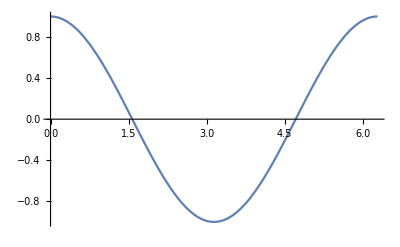

```mathematica
Plot[Cos[x],{x,0,2π}]
```

```mathematica
Plot3D[1-x^2-y^2,{x,-.5,.5},{y,-.5,.5}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{10 Sin[t],10 Cos[t],t},{t,0,20}]
```

-Graphics3D-

Mathematica also includes very effective methods of adding dynamic behaviour to graphs. For example, we might be interested in how the Bessel functions,  J_n(k x) depend on the index, n, and the scaling parameter, k:

```mathematica
Manipulate[Plot[BesselJ[n,k x],{x,0,3}],{n,0,4,1},{k,0,10}]
```

We can even animate the result by clicking the + button.

We can do the same for more complicated plots, but we must be prepared for the calculations to be a bit slower.

```mathematica
Manipulate[Plot3D[BesselJ[n,k Sqrt[x^2+y^2]],{x,-3,3},{y,-3,3}],{n,0,4,1},{k,0,10}]
```

## Summary

The important features of Mathematica that we have covered here, but which tend to cause problems, are:
  the significance of the different equals signs: = is the Set function,  == is the Equal function.
 Brackets [], (),{} and [[ ]] have quite specific uses, and if they are used in the wrong contexts will produce unexpected results.
 We have introduced quite a lot of Mathematica functions. You do not have to learn all of these -- the Mathematica help files are comprehensive and quite easy to use.

A.H. Harker, Junderwood. J. Bhamrah
UCL
January 2009, revised January 2011, January 2015, October 2018, January 2020